```mathematica
it = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ)∫_(d/2 - a/2)^(d/2+a/2) E^((2 π I (w-y1)^2)/(2 * D1 * λ))*E^((2 π I (y1-z)^2)/(2 * D2 * λ))ⅆy1;
ib = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ) ∫_(-d/2-a/2)^(-d/2+a/2) E^((2 π I (w-y2)^2)/(2 * D1 * λ))*E^((2 π I (y2-z)^2)/(2 * D2 * λ))ⅆy2;
```

```mathematica
i = (it + ib);
coni = Conjugate[i];
func = i*coni;
```

```mathematica
D1 = 380;
D2 = 500;
λ = .000546;
z = x -6.2;
d = .353;
a = .1;
```

```mathematica
func;
realfunc = 9000*Re[func];
```

```mathematica
SetDirectory["/Users/danikaluntz-martin/Desktop/Advanced Lab/DoubleSlit-ED"];
counts1 = Import["2014_double_slit_bulb_counts.csv"];
counts1;
```

```mathematica
fit1 = NonlinearModelFit[counts1,realfunc,{{w,0}}, x];
```

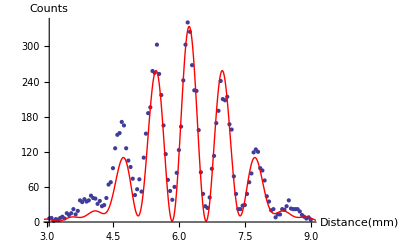

```mathematica
plot1 = Plot[fit1[x], {x, 0, 10},PlotRange->All, PlotStyle->Red];
Show[ListPlot[counts1], plot1,AxesLabel-> {Distance  [mm],Counts}]
```

```mathematica
fit1["FitResiduals"];
```

```mathematica
ChiSq=∑_(j=1)^120 ((fit1["FitResiduals"][[j]])/(2(√counts1[[j,2]]-√1.68)))^2
```

374.246

```mathematica
RedChiSq = ChiSq/7
```

53.4637